# Interpolación de Hermite

## Generación de puntos

```mathematica
D[x Sin[2x],x]
```

2 x Cos[2 x]+Sin[2 x]

```mathematica
a = 1; b = 4;
fList = Table[{x,N[x Sin[2x]]},{x,a,b,1}]
fPrimeList = Table[{x,N[2 x Cos[2 x]+Sin[2 x]]},{x,a,b,1}]
```

{{1,0.909297},{2,-1.5136},{3,-0.838246},{4,3.95743}}

{{1,0.0770038},{2,-3.37138},{3,5.48161},{4,-0.174642}}

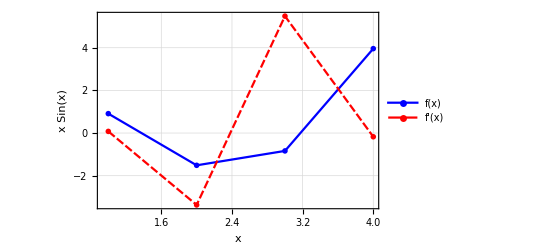

```mathematica
ListLinePlot[{fList,fPrimeList},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["x Sin(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue,Red},PlotLegends->{"f(x)","f'(x)"}
]
```

## Base de Lagrange

```mathematica
LagrangeBaseElements[xs_,i_]:=Table[If[i≠ j,(x-xs[[j+1]])/(xs[[i+1]]-xs[[j+1]]),1],{j,0,Length[xs]-1}];
LagrangeBase[xs_,i_]:=Apply[Times,LagrangeBaseElements[xs,i]];
```

```mathematica
LagrangeBase[fList[[All,1]],0]
```

1/6 (2-x) (3-x) (4-x)

## Base de Hermite

```mathematica
HermiteAlphaBase[xs_,i_]:=(1-2 D[LagrangeBase[xs,i],x](x-xs[[i+1]])) LagrangeBase[xs,i]^2;
HermiteBetaBase[xs_,i_]:=(x-xs[[i+1]]) LagrangeBase[xs,i]^2;
```

```mathematica
HermiteAlphaBase[fList[[All,1]],0]
```

1/36 (1-2 (-1/6 (2-x) (3-x)-1/6 (2-x) (4-x)-1/6 (3-x) (4-x)) (-1+x)) (2-x)^2 (3-x)^2 (4-x)^2

```mathematica
HermiteBetaBase[fPrimeList[[All,1]],0]
```

1/36 (2-x)^2 (3-x)^2 (4-x)^2 (-1+x)

## Interpolación de Hermite

```mathematica
HermiteInterpolate[fList_,fPrimeList_]:=Expand[fList[[All,2]].Table[HermiteAlphaBase[fList[[All,1]],i],{i,0,Length[fList]-1}]]+Expand[fPrimeList[[All,2]].Table[HermiteBetaBase[fPrimeList[[All,1]],i],{i,0,Length[fPrimeList]-1}]];
```

```mathematica
hermite = HermiteInterpolate[fList,fPrimeList]
```

-1645.66+7102.41 x-12963. x^2+13150.9 x^3-8188.74 x^4+3251.51 x^5-824.706 x^6+129.01 x^7-11.2995 x^8+0.421848 x^9

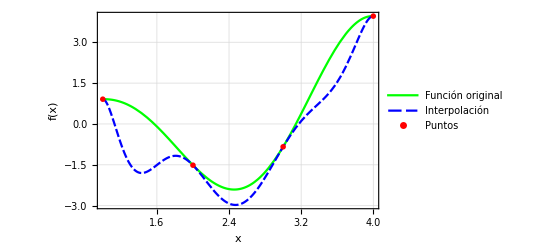

```mathematica
Show[
Plot[
{x Sin[2x],hermite},
{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green,Blue},PlotLegends->{"Función original","Interpolación"}
],
ListPlot[fList,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

## Comparación con Interpolación de Lagrange

```mathematica
LagrangeInterpolate[data_]:=Expand[data[[All,2]].Table[LagrangeBase[data[[All,1]],i],{i,0,Length[data]-1}]];
```

```mathematica
lagrange = LagrangeInterpolate[fList]
```

5.4084-5.19652 x+0.52707 x^2+0.170343 x^3

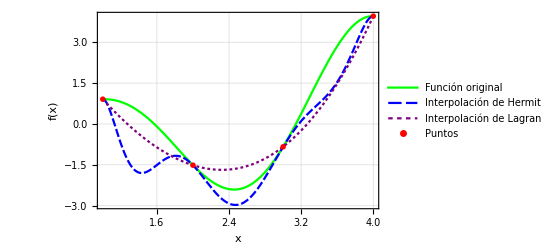

```mathematica
Show[
Plot[
{x Sin[2x],hermite, lagrange},
{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green,Blue,Purple},PlotLegends->{"Función original","Interpolación de Hermite","Interpolación de Lagrange"}
],
ListPlot[fList,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

## Analisis del error

```mathematica
RHermite[x_]:=x Sin[2x]-hermite;
RLagrange[x_]:=x Sin[2x]-lagrange;
```

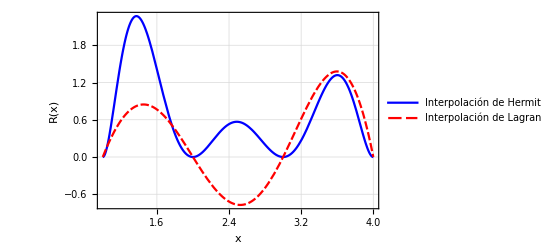

```mathematica
Plot[{RHermite[x],RLagrange[x]},{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["R(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue,Red},PlotLegends->{"Interpolación de Hermite", "Interpolación de Lagrange"}]
```

```mathematica
ϵHermite = √NIntegrate[RHermite[x]^2,{x,a,b}]
```

1.63675

```mathematica
ϵLagrange = √NIntegrate[RLagrange[x]^2,{x,a,b}]
```

1.27104